```mathematica
<<VilCretas`
```

VilCretas está disponible.

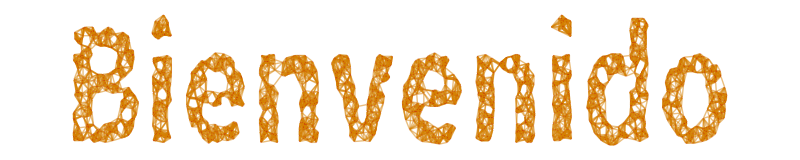

```mathematica
GrafoString["Bienvenido"]
```

```mathematica
nodos={e,g,a,h,b,f,d,c};
grafo=Grafo[{{a,b},{a,c},{a,d},{a,e},{b,g},{b,h},{c,e},{c,f},{c,g},{d,e},{d,f},{d,g},{d,h},{e,f},{e,g},{e,h},{f,h}},pesos->-{8,4,1,3,10,10,1,4,4,7,6,10,7,1,7,8,3},mostrarpesos->True];
Kruskal[grafo];
```

T={d<->g,b<->h,b<->g,a<->b,e<->h,d<->f,a<->c}

Peso: -56

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
Prim[grafo,orden->nodos]
```

El orden de los nodos es: {e,g,a,h,b,f,d,c}

T={{e,h},{h,b},{b,g},{g,d},{b,a},{d,f},{g,c}}

Peso: -56

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

```mathematica
gr1=Grafo[{{a,f},{a,g},{a,h},{a,j},{b,c},{b,d},{b,e},{b,h},{b,i},{c,e},{d,f},{e,f},{f,g},{f,j},{i,j}},pesos->-{15,3,16,49,32,41,43,3,1,49,25,28,9,11,48},mostrarpesos->True];
```

```mathematica
AlDijkstra[gr1, a,g, all->True]
```

Tabla de pesos del grafo

| a | f | g | h | j | b | c | d | e | i
a | 0 | -15 | -3 | -16 | -49 | 0 | 0 | 0 | 0 | 0
f | -15 | 0 | -9 | 0 | -11 | 0 | 0 | -25 | -28 | 0
g | -3 | -9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
h | -16 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | 0
j | -49 | -11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -48
b | 0 | 0 | 0 | -3 | 0 | 0 | -32 | -41 | -43 | -1
c | 0 | 0 | 0 | 0 | 0 | -32 | 0 | 0 | -49 | 0
d | 0 | -25 | 0 | 0 | 0 | -41 | 0 | 0 | 0 | 0
e | 0 | -28 | 0 | 0 | 0 | -43 | -49 | 0 | 0 | 0
i | 0 | 0 | 0 | 0 | -48 | -1 | 0 | 0 | 0 | 0

Inicialización: {{a,0,{}},{f,∞,{}},{g,∞,{}},{h,∞,{}},{j,∞,{}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,∞,{}}}

Se seleccionó el nodo: a

Lista actual de vértices: {f,g,h,j,b,c,d,e,i}

Lista actual de marcas: {{f,-15,{a}},{g,-3,{a}},{h,-16,{a}},{j,-49,{a}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,∞,{}}}

Se seleccionó el nodo: j

Lista actual de vértices: {f,g,h,b,c,d,e,i}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-16,{a}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,-97,{j}}}

Se seleccionó el nodo: i

Lista actual de vértices: {f,g,h,b,c,d,e}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-16,{a}},{b,-98,{i}},{c,∞,{}},{d,∞,{}},{e,∞,{}}}

Se seleccionó el nodo: b

Lista actual de vértices: {f,g,h,c,d,e}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-101,{b}},{c,-130,{b}},{d,-139,{b}},{e,-141,{b}}}

Se seleccionó el nodo: e

Lista actual de vértices: {f,g,h,c,d}

Lista actual de marcas: {{f,-169,{e}},{g,-3,{a}},{h,-101,{b}},{c,-190,{e}},{d,-139,{b}}}

Se seleccionó el nodo: c

Lista actual de vértices: {f,g,h,d}

Lista actual de marcas: {{f,-169,{e}},{g,-3,{a}},{h,-101,{b}},{d,-139,{b}}}

Se seleccionó el nodo: f

Lista actual de vértices: {g,h,d}

Lista actual de marcas: {{g,-178,{f}},{h,-101,{b}},{d,-194,{f}}}

Se seleccionó el nodo: d

Lista actual de vértices: {g,h}

Lista actual de marcas: {{g,-178,{f}},{h,-101,{b}}}

Se seleccionó el nodo: g

La longitud de un camino más corto es: -178

Lista actual de vértices: {h}

Lista actual de marcas: {{h,-101,{b}}}

Iteraciones: (a | f | g | h | j | b | c | d | e | i
{0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{0,{}} | {-15,{a}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {-97,{j}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {-98,{i}} | {∞,{}} | {∞,{}} | {∞,{}} | {-97,{j}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-130,{b}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}})

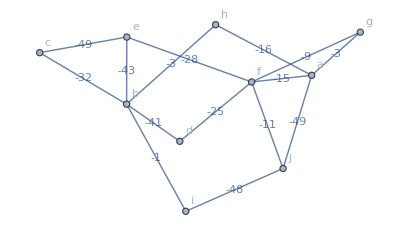

```mathematica
gr1
```

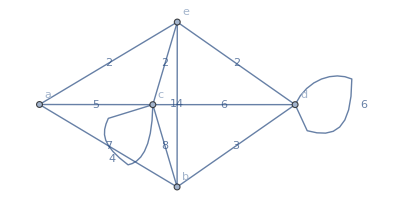

```mathematica
aristas={{a,b},{a,c},{a,e},{b,c},{b,d},{b,e},{c,d},{c,e},{d,d},{c,c},{d,e}};
pes={7,5,2,8,3,14,6,2,6,4,2};
gra1 = Grafo[aristas, pesos->pes, mostrarpesos->True]
```

```mathematica
Valencias[gra1]
```

| a | b | c | e | d
Grado o valencia | 3 | 4 | 6 | 4 | 5

```mathematica
?MPGrafo
```

```mathematica
MPGrafo[gra1, {a,b,c,d,e}, table->True]
```

| a | b | c | d | e
a | 0 | 7 | 5 | 0 | 2
b | 7 | 0 | 8 | 3 | 14
c | 5 | 8 | 4 | 6 | 2
d | 0 | 3 | 6 | 6 | 2
e | 2 | 14 | 2 | 2 | 0

```mathematica
ListaVertices[gra1]
```

{a,b,c,d,e}

```mathematica
CantAristas[gra1]
```

11

Matriz de incidencia

```mathematica
?MIGrafo
```

```mathematica
MIGrafo[gra1,{a,b,c,d,e}, table->True]
```

| a<->b | a<->c | a<->e | b<->c | b<->d | b<->e | c<->d | c<->e | d<->d | c<->c | d<->e
a | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
b | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
c | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
d | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
e | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1

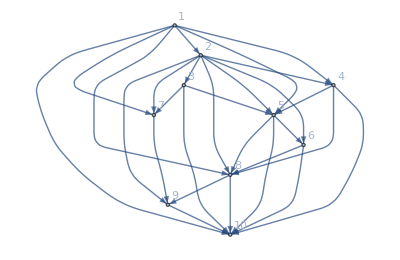

```mathematica
arist ={{1,2},{1,4},{1,5},{1,7},{1,8},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,5},{3,7},{3,10},{4,5},{4,8},{4,10},{5,6},{5,8},{5,10},{6,8},{6,10},{7,9},{8,9},{8,10},{9,10}};
gra2=Grafo[arist, dirigido->True, vertices->Range[10]]
```

```mathematica
Valencias[gra2]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
Grado o valencia interna | 0 | 1 | 1 | 2 | 4 | 2 | 3 | 5 | 3 | 7
Grado o valencia externa | 6 | 7 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 0

Hamilton y Euler
K_(1000, 1000) ->Knm

K_1000 -> Kn
Luego ver si es circuito o ruta, y por ultimo ver si es Hamilton o Euler

```mathematica
KnCircuitoHamiltonQ
KnCircuitoEulerQ
KnRutaHamiltonQ
KnRutaEulerQ

KnmCircuitoEulerQ
KnmCircuitoHamiltonQ
KnmRutaEulerQ
KnmRutaHamiltonQ
```

```mathematica
KnmCircuitoHamiltonQ[500,500]
```

True

```mathematica
KnCircuitoEulerQ[21534]
```

False

```mathematica
KnCircuitoHamiltonQ[14147]&&KnRutaHamiltonQ[14147]
```

True

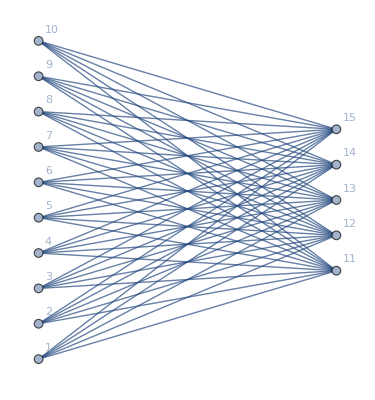

```mathematica
GrafoBipartitoCompleto[10,5]
```

```mathematica
ArbolQ[GrafoBipartitoCompleto[10,5]]
```

False

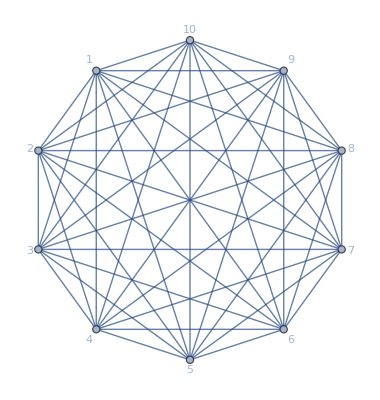

```mathematica
GrafoCompleto[10]
```

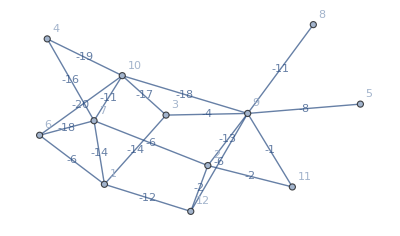

```mathematica
grafo=Grafo[{{1,3},{1,6},{1,7},{1,12},{2,7},{2,9},{2,11},{2,12},{3,9},{3,10},{4,7},{4,10},{5,9},{6,7},{6,10},{7,10},{8,9},{9,10},{9,11},{9,12}},pesos->-1 {14,6,14,12,6,13,2,2,4,17,16,19,8,18,20,11,11,18,1,6},mostrarpesos->True]
```

```mathematica
AlDijkstra[grafo, 6,8]
```

La longitud de un camino más corto es: -98

Iteraciones: (1 | 3 | 6 | 7 | 12 | 2 | 9 | 11 | 10 | 4 | 5 | 8
{∞,{}} | {∞,{}} | {0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{-6,{6}} | {∞,{}} | {0,{}} | {-18,{6}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {-20,{6}} | {∞,{}} | {∞,{}} | {∞,{}}
{-6,{6}} | {-37,{10}} | {0,{}} | {-31,{10}} | {∞,{}} | {∞,{}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-6,{6}} | {-37,{10}} | {0,{}} | {-55,{4}} | {∞,{}} | {∞,{}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-37,{10}} | {0,{}} | {-55,{4}} | {∞,{}} | {-61,{7}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-81,{1}} | {-61,{7}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-81,{1}} | {-61,{7}} | {-87,{3}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-93,{9}} | {-100,{9}} | {-87,{3}} | {-88,{9}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}})

```mathematica
AlDijkstra[grafo, 6,8, all->True]
```

Tabla de pesos del grafo

| 1 | 3 | 6 | 7 | 12 | 2 | 9 | 11 | 10 | 4 | 5 | 8
1 | 0 | -14 | -6 | -14 | -12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | -14 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | -17 | 0 | 0 | 0
6 | -6 | 0 | 0 | -18 | 0 | 0 | 0 | 0 | -20 | 0 | 0 | 0
7 | -14 | 0 | -18 | 0 | 0 | -6 | 0 | 0 | -11 | -16 | 0 | 0
12 | -12 | 0 | 0 | 0 | 0 | -2 | -6 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | -6 | -2 | 0 | -13 | -2 | 0 | 0 | 0 | 0
9 | 0 | -4 | 0 | 0 | -6 | -13 | 0 | -1 | -18 | 0 | -8 | -11
11 | 0 | 0 | 0 | 0 | 0 | -2 | -1 | 0 | 0 | 0 | 0 | 0
10 | 0 | -17 | -20 | -11 | 0 | 0 | -18 | 0 | 0 | -19 | 0 | 0
4 | 0 | 0 | 0 | -16 | 0 | 0 | 0 | 0 | -19 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0 | 0 | 0 | -8 | 0 | 0 | 0 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0 | -11 | 0 | 0 | 0 | 0 | 0

Inicialización: {{1,∞,{}},{3,∞,{}},{6,0,{}},{7,∞,{}},{12,∞,{}},{2,∞,{}},{9,∞,{}},{11,∞,{}},{10,∞,{}},{4,∞,{}},{5,∞,{}},{8,∞,{}}}

Se seleccionó el nodo: 6

Lista actual de vértices: {1,3,7,12,2,9,11,10,4,5,8}

Lista actual de marcas: {{1,-6,{6}},{3,∞,{}},{7,-18,{6}},{12,∞,{}},{2,∞,{}},{9,∞,{}},{11,∞,{}},{10,-20,{6}},{4,∞,{}},{5,∞,{}},{8,∞,{}}}

Se seleccionó el nodo: 10

Lista actual de vértices: {1,3,7,12,2,9,11,4,5,8}

Lista actual de marcas: {{1,-6,{6}},{3,-37,{10}},{7,-31,{10}},{12,∞,{}},{2,∞,{}},{9,-38,{10}},{11,∞,{}},{4,-39,{10}},{5,∞,{}},{8,∞,{}}}

Se seleccionó el nodo: 4

Lista actual de vértices: {1,3,7,12,2,9,11,5,8}

Lista actual de marcas: {{1,-6,{6}},{3,-37,{10}},{7,-55,{4}},{12,∞,{}},{2,∞,{}},{9,-38,{10}},{11,∞,{}},{5,∞,{}},{8,∞,{}}}

Se seleccionó el nodo: 7

Lista actual de vértices: {1,3,12,2,9,11,5,8}

Lista actual de marcas: {{1,-69,{7}},{3,-37,{10}},{12,∞,{}},{2,-61,{7}},{9,-38,{10}},{11,∞,{}},{5,∞,{}},{8,∞,{}}}

Se seleccionó el nodo: 1

Lista actual de vértices: {3,12,2,9,11,5,8}

Lista actual de marcas: {{3,-83,{1}},{12,-81,{1}},{2,-61,{7}},{9,-38,{10}},{11,∞,{}},{5,∞,{}},{8,∞,{}}}

Se seleccionó el nodo: 3

Lista actual de vértices: {12,2,9,11,5,8}

Lista actual de marcas: {{12,-81,{1}},{2,-61,{7}},{9,-87,{3}},{11,∞,{}},{5,∞,{}},{8,∞,{}}}

Se seleccionó el nodo: 9

Lista actual de vértices: {12,2,11,5,8}

Lista actual de marcas: {{12,-93,{9}},{2,-100,{9}},{11,-88,{9}},{5,-95,{9}},{8,-98,{9}}}

Se seleccionó el nodo: 2

Lista actual de vértices: {12,11,5,8}

Lista actual de marcas: {{12,-102,{2}},{11,-102,{2}},{5,-95,{9}},{8,-98,{9}}}

Se seleccionó el nodo: 12

Lista actual de vértices: {11,5,8}

Lista actual de marcas: {{11,-102,{2}},{5,-95,{9}},{8,-98,{9}}}

Se seleccionó el nodo: 11

Lista actual de vértices: {5,8}

Lista actual de marcas: {{5,-95,{9}},{8,-98,{9}}}

Se seleccionó el nodo: 8

La longitud de un camino más corto es: -98

Lista actual de vértices: {5}

Lista actual de marcas: {{5,-95,{9}}}

Iteraciones: (1 | 3 | 6 | 7 | 12 | 2 | 9 | 11 | 10 | 4 | 5 | 8
{∞,{}} | {∞,{}} | {0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{-6,{6}} | {∞,{}} | {0,{}} | {-18,{6}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {-20,{6}} | {∞,{}} | {∞,{}} | {∞,{}}
{-6,{6}} | {-37,{10}} | {0,{}} | {-31,{10}} | {∞,{}} | {∞,{}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-6,{6}} | {-37,{10}} | {0,{}} | {-55,{4}} | {∞,{}} | {∞,{}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-37,{10}} | {0,{}} | {-55,{4}} | {∞,{}} | {-61,{7}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-81,{1}} | {-61,{7}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-81,{1}} | {-61,{7}} | {-87,{3}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-93,{9}} | {-100,{9}} | {-87,{3}} | {-88,{9}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}})

Inicio a Fin: 6->10->4->7->1->3->9->8
Fin a Inicio: 8->9->3->1->7->4->10->6
Recordar en la longitud usar el valor absoluto: |-n| -> n

Error común

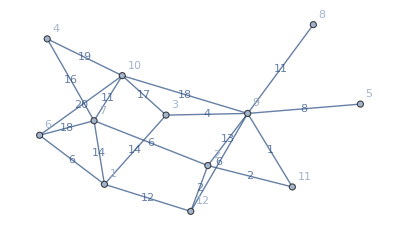

```mathematica
grafo2=Grafo[{{1,3},{1,6},{1,7},{1,12},{2,7},{2,9},{2,11},{2,12},{3,9},{3,10},{4,7},{4,10},{5,9},{6,7},{6,10},{7,10},{8,9},{9,10},{9,11},{9,12}},pesos->{14,6,14,12,6,13,2,2,4,17,16,19,8,18,20,11,11,18,1,6},mostrarpesos->True]
```

```mathematica
AlDijkstra[grafo2, 6,8]
```

La longitud de un camino más corto es: 34

Iteraciones: (1 | 3 | 6 | 7 | 12 | 2 | 9 | 11 | 10 | 4 | 5 | 8
{∞,{}} | {∞,{}} | {0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{6,{6}} | {∞,{}} | {0,{}} | {18,{6}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {20,{6}} | {∞,{}} | {∞,{}} | {∞,{}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {∞,{}} | {∞,{}} | {∞,{}} | {20,{6}} | {∞,{}} | {∞,{}} | {∞,{}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {24,{7}} | {∞,{}} | {∞,{}} | {20,{6}} | {34,{7}} | {∞,{}} | {∞,{}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {24,{12}} | {∞,{}} | {20,{6}} | {34,{7}} | {∞,{}} | {∞,{}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {24,{12,3}} | {∞,{}} | {20,{6}} | {34,{7}} | {∞,{}} | {∞,{}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {24,{12,3}} | {22,{2}} | {20,{6}} | {34,{7}} | {∞,{}} | {∞,{}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {24,{12,3}} | {22,{2}} | {20,{6}} | {34,{7}} | {∞,{}} | {∞,{}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {23,{11}} | {22,{2}} | {20,{6}} | {34,{7}} | {∞,{}} | {∞,{}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {23,{11}} | {22,{2}} | {20,{6}} | {34,{7}} | {31,{9}} | {34,{9}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {23,{11}} | {22,{2}} | {20,{6}} | {34,{7}} | {31,{9}} | {34,{9}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {23,{11}} | {22,{2}} | {20,{6}} | {34,{7}} | {31,{9}} | {34,{9}}
{6,{6}} | {20,{1}} | {0,{}} | {18,{6}} | {18,{1}} | {20,{12}} | {23,{11}} | {22,{2}} | {20,{6}} | {34,{7}} | {31,{9}} | {34,{9}})

{34.,{{6,1},{1,12},{12,2},{2,11},{11,9},{9,8}}}

```mathematica
nodos={d,a,f,g,e,b,c,h};

grafo=Grafo[{{a,b},{a,d},{a,e},{a,f},{b,d},{b,e},{b,g},{b,h},{c,d},{c,f},{c,g},{c,h},{d,e},{e,f},{f,g},{f,h},{g,h}},pesos->{6,9,2,4,2,4,1,9,1,8,2,4,4,3,9,3,2},mostrarpesos->True];
```

```mathematica
?BuscarPrimeroAncho
?BuscarPrimeroLargo
```

```mathematica
BuscarPrimeroLargo[grafo, animacion->True, orden->nodos]
```

{{d,a},{a,f},{f,g},{g,b},{e,b},{b,h},{c,h}}

```mathematica
BuscarPrimeroAncho[grafo, animacion->True, orden->nodos]
```

{{d,a},{d,e},{d,b},{d,c},{a,f},{g,b},{b,h}}

```mathematica
nodos
```

{d,a,f,g,e,b,c,h}

```mathematica
Sort/@{{d,a},{d,e},{d,b},{d,c},{a,f},{g,b},{b,h}}
```

{{a,d},{d,e},{b,d},{c,d},{a,f},{b,g},{b,h}}

```mathematica
matr=({{1, 0, 0, 0, 0}, {1, 1, 1, 1, 0}, {0, 0, 1, 0, 1}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
MGrafo[GrafoMI[matr,{a,b,c,d,e}],{a,b,c,d,e}]
```

(0 | 1 | 0 | 0 | 0
1 | 2 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
?MPGrafo
```

```mathematica
?MGrafo
```